```mathematica
(*gives n uniformly distributed points in a unit disk*)
randomDiskPoint[n_]:=With[{
circlePoints=Normalize/@RandomVariate[NormalDistribution[],{n,2}],
radii=RandomVariate[TriangularDistribution[{0,1},1],n]
},
#[[1]]#[[2]]&/@Transpose[{radii,circlePoints}]
];
```

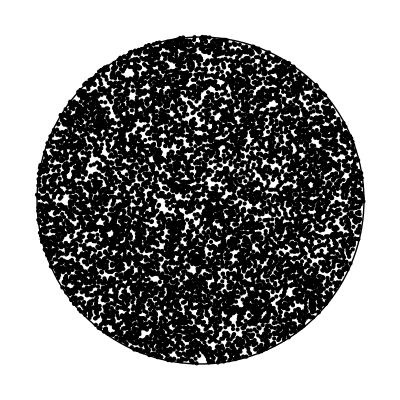

```mathematica
Graphics[{Point[randomDiskPoint[10000]],Circle[]}]
```

```mathematica
Needs["TriangleLink`"];
```

```mathematica
boundaryLength[points_]:=Length[TriangleConvexHull[points][[2]]];
```

```mathematica
(*triangle: {{x1,y1},{x2,y2},{x3,y3}}={v1_,v2_,v3_}
point: {x,y}=p
returns true if point is in the interior of the triangle*)
eps=10^-9;
pointInTriangleQ[{v1_,v2_,v3_},p_]:=If[
Det[{v2-v1,v3-v1}]Det[{v2-v1,p-v1}]>eps&&Det[{v3-v1,v2-v1}]Det[{v3-v1,p-v1}]>eps&&Det[{v3-v2,v1-v2}]Det[{v3-v2,p-v2}]>eps,
True,
False
];
```

```mathematica
(*returns true if no point from points is inside the triangle*)
triangleEmptyQ[triangle_,points_]:=Not@AnyTrue[pointInTriangleQ[triangle,#]&/@points,TrueQ];
```

```mathematica
(*todo: it can be done faster*)
emptyTriangles[points_]:=With[{triangles=Subsets[points,{3}]},
Select[triangles,triangleEmptyQ[#,points]&]
];
```

```mathematica
eps=10^-9;
segmentsIntersectQ[{p1_,p2_},{q1_,q2_}]:=If[
Det[{p2-p1,q1-p1}]Det[{p2-p1,q2-p1}]<-eps&&
Det[{q2-q1,p1-q1}]Det[{q2-q1,p2-q1}]<-eps,
True,
False
];
```

```mathematica
(*todo: corner cases*)
trianglesIntersectQ[t1_,t2_]:=segmentsIntersectQ[{t1[[1]],t1[[2]]},{t2[[1]],t2[[2]]}]||
segmentsIntersectQ[{t1[[1]],t1[[2]]},{t2[[1]],t2[[3]]}]||
segmentsIntersectQ[{t1[[1]],t1[[2]]},{t2[[3]],t2[[2]]}]||
segmentsIntersectQ[{t1[[1]],t1[[3]]},{t2[[1]],t2[[2]]}]||
segmentsIntersectQ[{t1[[1]],t1[[3]]},{t2[[1]],t2[[3]]}]||
segmentsIntersectQ[{t1[[1]],t1[[3]]},{t2[[3]],t2[[2]]}]||
segmentsIntersectQ[{t1[[3]],t1[[2]]},{t2[[1]],t2[[2]]}]||
segmentsIntersectQ[{t1[[3]],t1[[2]]},{t2[[1]],t2[[3]]}]||
segmentsIntersectQ[{t1[[3]],t1[[2]]},{t2[[3]],t2[[2]]}]||
pointInTriangleQ[t1,t2[[1]]]||
pointInTriangleQ[t1,t2[[2]]]||
pointInTriangleQ[t1,t2[[3]]]||
pointInTriangleQ[t2,t1[[1]]]||
pointInTriangleQ[t2,t1[[2]]]||
pointInTriangleQ[t2,t1[[3]]];
```

```mathematica
antiGraphTriangles[triangles_]:=Graph[
triangles,
#[[1]]<->#[[2]]&/@Select[Subsets[triangles,{2}],trianglesIntersectQ[#[[1]],#[[2]]]&]];
```

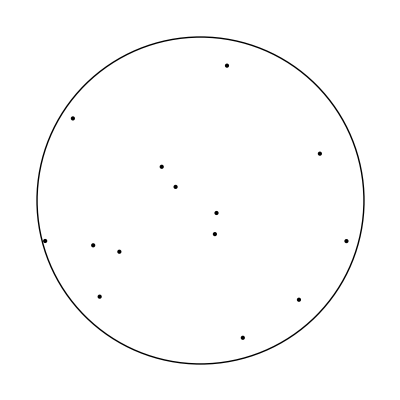

```mathematica
points=randomDiskPoint[14];
Graphics[{Point[points],Circle[]}]
g=antiGraphTriangles[emptyTriangles[points]];
```

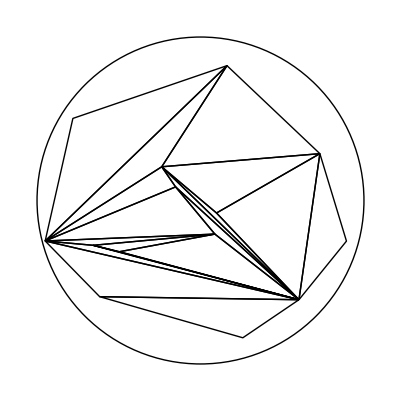

```mathematica
triangulation=FindIndependentVertexSet[g];
Graphics[
Append[
Line[#~Join~{First[#]}]&/@triangulation[[1]],
Circle[]
]
]
```

```mathematica
FindIndependentVertexSet[g,Infinity,10^10]//Length
```

330249

```mathematica
(*Do[stream=OpenAppend[NotebookDirectory[]<>"data-number-triangulations.csv"];
(*n=RandomInteger[{4,14}];*)
n=10;
Print[n," points"];
points=randomDiskPoint[n];
l=boundaryLength[points];
Print[l," boundary length"];
triangles=emptyTriangles[points];
Print[Length[triangles]," empty triangles"];
g=antiGraphTriangles[triangles];
numTriangulations=FindIndependentVertexSet[g,Infinity,10^10]//Length;
Print[numTriangulations," triangulations"];
Print["------------------------"];
Export[stream,{{n,l,Length[triangles],numTriangulations}},"CSV"];
Close[stream],
10]*)
```

17 points

7 boundary length

321 empty triangles

```mathematica
data=Import[NotebookDirectory[]<>"data/data-number-triangulations.csv"][[5;;]];
```

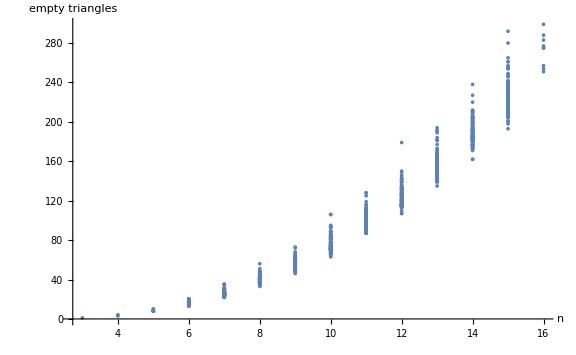

```mathematica
ListPlot[data[[All,{1,3}]],ImageSize->Large,LabelStyle->Medium,AxesLabel->{"n","empty triangles"}]
```

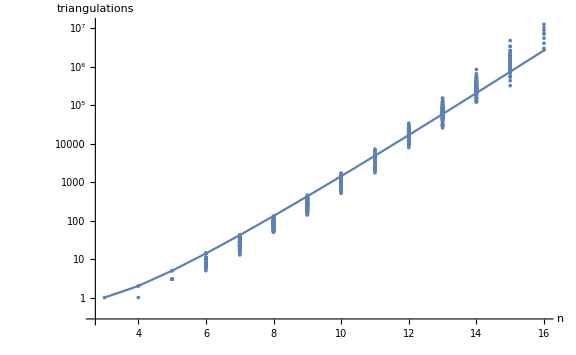

```mathematica
Show[
ListLogPlot[data[[All,{1,4}]],ImageSize->Large,LabelStyle->Medium,AxesLabel->{"n","triangulations"}],
ListLinePlot[Table[{n,Log@CatalanNumber[n-2]},{n,3,16}]]
]
```

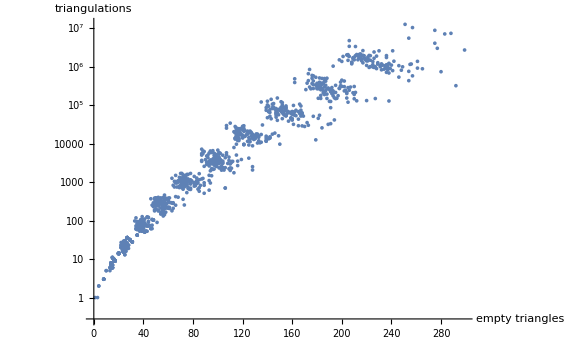

```mathematica
ListLogPlot[data[[All,{3,4}]],ImageSize->Large,LabelStyle->Medium,AxesLabel->{"empty triangles","triangulations"}]
```

```mathematica
points=Table[{Cos[f],Sin[f]},{f,0,2π-0.01,2π/5}]
Graphics[Point[points]]
(*Export[NotebookDirectory[]<>"instances/convex-5/points.csv",N[points]]*)
```

{{1,0},{1/4 (-1+√5),√(5/8+(√5)/8)},{1/4 (-1-√5),√(5/8-(√5)/8)},{1/4 (-1-√5),-√(5/8-(√5)/8)},{1/4 (-1+√5),-√(5/8+(√5)/8)}}

-Graphics-

/home/paul/Documents/Experiments/flip-graphs/instances/convex-5/points.csv

```mathematica
t=emptyTriangles[points]/.(#[[1]]->#[[2]]&/@Transpose[{points,Table[i,{i,0,4}]}])
(*Export[NotebookDirectory[]<>"instances/convex-5/triangles.csv",t]*)
```

{{0,1,2},{0,1,3},{0,1,4},{0,2,3},{0,2,4},{0,3,4},{1,2,3},{1,2,4},{1,3,4},{2,3,4}}

/home/paul/Documents/Experiments/flip-graphs/instances/convex-5/triangles.csv

```mathematica
g=antiGraphTriangles[emptyTriangles[points]];
triangulation=FindIndependentVertexSet[g]/.(#[[1]]->#[[2]]&/@Transpose[{emptyTriangles[points],Table[i,{i,0,9}]}])
(*Export[NotebookDirectory[]<>"instances/convex-5/initial-triangulation.csv",triangulation]*)
```

{{0,3,5}}

/home/paul/Documents/Experiments/flip-graphs/instances/convex-5/initial-triangulation.csv